## VertexCut

```mathematica
VertexCut[g_?UndirectedGraphQ,parm___]:=VertexCut[DirectedGraph[g],parm]
```

```mathematica
VertexCut[g_?MultigraphQ,parm___]:=VertexCut[SimpleGraph[g],parm]
```

```mathematica
VertexCut[g:Except[_?LoopFreeGraphQ],parm___]:=VertexCut[SimpleGraph[g],parm]
```

```mathematica
VertexCut[g_?DirectedGraphQ]:=
Block[{res,n,m,a,b,u,v},
n=VertexCount[g];(*I understand this line*)
m=Transpose[IncidenceMatrix[g]];(*I don't understand what this line is for I understand what the incidence matrix represents and what the transpose of a matrix represents but I don't understand what this does.*)
a=UnitStep[m-1];(*remove negative values from directed edges/arcs.*)
b=a-m;(*constraints*)
res=LinearOptimization[-Total[u+v](*I understand this objective function and the linear optimization*),{u+v \[VectorLessEqual]1(*I understand this as saying *),a.u +b.v\[VectorLessEqual]1,a.v +b.u\[VectorLessEqual]1,Total[u]\[VectorGreaterEqual]1,Total[v]\[VectorGreaterEqual]1,u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0,u\[VectorLessEqual]1,v\[VectorLessEqual]1},{u∈Vectors[n,Integers],v∈Vectors[n,Integers]}];
VertexList[g][[Flatten[Position[Total[{u,v} /. res],0]]]] 
]
```

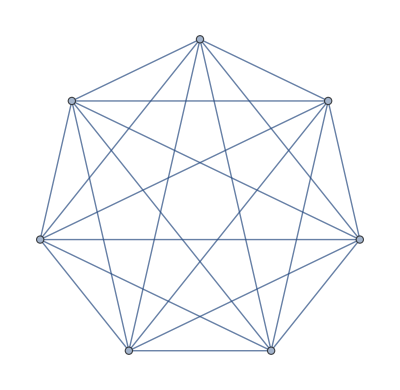

```mathematica
RandomGraph[{7,21}]
```

```mathematica
IncidenceMatrix[RandomGraph[{7,21}]]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1)

```mathematica
Transpose@IncidenceMatrix[RandomGraph[{7,21}]]//MatrixForm
```

(1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1)

#### Undirected Graph

```mathematica
Transpose@IncidenceMatrix[RandomGraph[{7,21}]]//Normal
```

{{1,1,0,0,0,0,0},{1,0,1,0,0,0,0},{1,0,0,1,0,0,0},{1,0,0,0,1,0,0},{1,0,0,0,0,1,0},{1,0,0,0,0,0,1},{0,1,1,0,0,0,0},{0,1,0,1,0,0,0},{0,1,0,0,1,0,0},{0,1,0,0,0,1,0},{0,1,0,0,0,0,1},{0,0,1,1,0,0,0},{0,0,1,0,1,0,0},{0,0,1,0,0,1,0},{0,0,1,0,0,0,1},{0,0,0,1,1,0,0},{0,0,0,1,0,1,0},{0,0,0,1,0,0,1},{0,0,0,0,1,1,0},{0,0,0,0,1,0,1},{0,0,0,0,0,1,1}}

```mathematica
UnitStep[Transpose@IncidenceMatrix[RandomGraph[{7,21}]]-1]//Normal
```

{{1,1,0,0,0,0,0},{1,0,1,0,0,0,0},{1,0,0,1,0,0,0},{1,0,0,0,1,0,0},{1,0,0,0,0,1,0},{1,0,0,0,0,0,1},{0,1,1,0,0,0,0},{0,1,0,1,0,0,0},{0,1,0,0,1,0,0},{0,1,0,0,0,1,0},{0,1,0,0,0,0,1},{0,0,1,1,0,0,0},{0,0,1,0,1,0,0},{0,0,1,0,0,1,0},{0,0,1,0,0,0,1},{0,0,0,1,1,0,0},{0,0,0,1,0,1,0},{0,0,0,1,0,0,1},{0,0,0,0,1,1,0},{0,0,0,0,1,0,1},{0,0,0,0,0,1,1}}

#### Directed Graph

```mathematica
randomDirectedGraph=RandomGraph[{7,21},DirectedEdges->True]
```

-Graphics-

```mathematica
m=Transpose@IncidenceMatrix[randomDirectedGraph]//Normal
```

{{-1,0,0,1,0,0,0},{-1,0,0,0,0,1,0},{1,-1,0,0,0,0,0},{0,-1,1,0,0,0,0},{0,-1,0,1,0,0,0},{0,-1,0,0,1,0,0},{0,-1,0,0,0,1,0},{1,0,-1,0,0,0,0},{0,1,-1,0,0,0,0},{0,0,-1,0,1,0,0},{0,0,1,-1,0,0,0},{0,0,0,-1,1,0,0},{0,0,0,-1,0,0,1},{1,0,0,0,-1,0,0},{0,1,0,0,-1,0,0},{0,0,1,0,-1,0,0},{0,0,0,0,-1,1,0},{0,0,0,0,-1,0,1},{1,0,0,0,0,-1,0},{0,0,1,0,0,0,-1},{0,0,0,0,0,1,-1}}

```mathematica
a=UnitStep[Transpose@IncidenceMatrix[randomDirectedGraph]-1]//Normal
```

{{0,0,0,1,0,0,0},{0,0,0,0,0,1,0},{1,0,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,1,0,0},{0,0,0,0,0,1,0},{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,0,0,1,0,0},{0,0,1,0,0,0,0},{0,0,0,0,1,0,0},{0,0,0,0,0,0,1},{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,0,1},{1,0,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,0,0,1,0}}

```mathematica
a-m
```

{{1,0,0,0,0,0,0},{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,1,0,0,0,0,0},{0,1,0,0,0,0,0},{0,1,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,1,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,1,0,0},{0,0,0,0,1,0,0},{0,0,0,0,1,0,0},{0,0,0,0,1,0,0},{0,0,0,0,1,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1}}

## Objective Cost Consideration

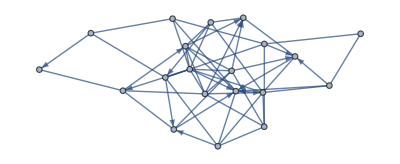

```mathematica
randomWeightedMixedGraph=RandomWeightedMixedGraph[{20,54},.5,RandomReal[{1,ⅇ},#]&]
```

```mathematica
AnnotationValue[randomWeightedMixedGraph,EdgeWeight]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
WeightedAdjacencyMatrix[randomWeightedMixedGraph]//MatrixForm
```

(0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
AnnotationValue[{randomWeightedMixedGraph,1->2},EdgeWeight]
```

$Failed

```mathematica
AnnotationValue[{randomWeightedMixedGraph,1<->6},EdgeWeight]
```

1.14076

```mathematica
Position[WeightedAdjacencyMatrix[randomWeightedMixedGraph]//Normal,AnnotationValue[{randomWeightedMixedGraph,1<->6},EdgeWeight]]
```

{{1,3}}

```mathematica
VertexList[randomWeightedMixedGraph]
```

{1,2,3,4,5,6,7}

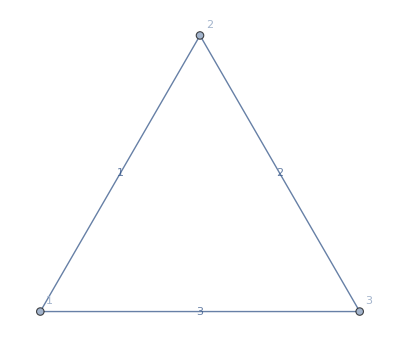

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeWeight->{1,2,3},VertexLabels->"Name",EdgeLabels->"EdgeWeight"]
```

```mathematica
WeightedAdjacencyMatrix[%]//MatrixForm
```

(0 | 1 | 3
1 | 0 | 2
3 | 2 | 0)

```mathematica
objective=cost Total[u+v]
```

```mathematica
secondConstraint=u+v \[VectorGreaterEqual]1
```

u+v\[VectorGreaterEqual]1

```mathematica
thirdConstraint=u\[VectorGreaterEqual]0
```

u\[VectorGreaterEqual]0

```mathematica
fourthConstraint=v\[VectorGreaterEqual]0
```

v\[VectorGreaterEqual]0

```mathematica
DirectedGraphArcs[RandomMixedGraph[{8,21},.5]]
```

{1->3,2->6,2->4,2->7,2->5,3->5,4->5,5->8,5->7,6->8}

### Simple Case

```mathematica
Block[{vertexCount,edgeData,formatDirectedEdgesData,edgeDifferenceData},vertexCount=VertexCount[randomWeightedMixedGraph];edgeData=Transpose[IncidenceMatrix[randomWeightedMixedGraph]];
formatDirectedEdgesData=UnitStep[edgeData-1];(*remove negative values from directed edges/arcs.*)
edgeDifferenceData=formatDirectedEdgesData-edgeData;(*constraints*)LinearOptimization[-Total[u+v](*I understand this objective function and the linear optimization*),{u+v \[VectorGreaterEqual]1(*I understand this as saying *),u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0},{u∈Vectors[vertexCount,Integers],v∈Vectors[vertexCount,Integers]}]
 ]
```

LinearOptimization::ubnd: The problem is unbounded.

{u→{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},v→{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}}

```mathematica
LinearOptimization[-Total[u+v],{secondConstraint,thirdConstraint,fourthConstraint},{u∈Vectors[n,Integers],v∈Vectors[n,Integers]}]
```

LinearOptimization::varspec: u∈Vectors[n,] is not a valid variable specification.

LinearOptimization[-Total[u+v],{u+v\[VectorLessEqual]1,u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0},{u∈Vectors[n,ℤ],v∈Vectors[n,ℤ]}]

```mathematica
LinearOptimization[-objective,constraints,variables]
```

```mathematica
VertexCut[g_?DirectedGraphQ,s_,t_] /; VertexQ[g,s]&&VertexQ[g,t]:=
Block[{res,n,m,a,b,u,v,i,j},
n=VertexCount[g];
m=Transpose[IncidenceMatrix[g]];
a=UnitStep[m-1];
b=a-m;
i=VertexIndex[g,s];
j=VertexIndex[g,t];
res=LinearOptimization[-Total[u+v],{u+v \[VectorLessEqual]1,a.u +b.v\[VectorLessEqual]1,a.v +b.u\[VectorLessEqual]1,Total[u]\[VectorGreaterEqual]1,Total[v]\[VectorGreaterEqual]1,u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0,u\[VectorLessEqual]1,v\[VectorLessEqual]1,Indexed[u,i]==1,Indexed[u,j]==0,Indexed[v,i]==0,Indexed[v,j]==1},{u∈Vectors[n,Integers],v∈Vectors[n,Integers]}];
VertexList[g][[Flatten[Position[Total[{u,v} /. res],0]]]] 
]
```

```mathematica
VertexCut[RandomGraph[{5,10}]]
```

LinearOptimization::nsolc: There are no points that satisfy the constraints.

{}

## Example

```mathematica
edges={start->F201,F201->Q,start->F202,F202->Q,Q->P,start->F203,F203->P,P->B21,F203->B21,start->F204,F204->B21,start->F205,F205->B21,start->F206,F206->B21,start->F207,F207->C21,C211->C21,F207->C211,C212->C21,start->C213,C213->C21,C21->B21,B21->H21,C21->H21,H21->H211,start->FH211,FH211->H211,C211->H211,H211->IH2111,IH2111->goal,start->L21,L21->C21,B21->L21,C21->D1,C212->D1,B21->D1,D1->E22,C211->E22,start->FE22,FE22->E22,E22->E221,start->FE221,FE221->E221,E22->K3123,K3123->goal,E221->MR,MR->goal,B21->G21,start->FG21T1,FG21T1->G21,start->FG21T2,FG21T2->G21,G21->G211,G211->X,X->goal,B21->K31,C21->K31,C212->K31,K31->K3111,K3111->Y,Y->goal,B21->J31,C21->J31,C211->J31,start->FJ311,FJ311->J31,start->FJ312,FJ312->J31,J31->J311,J311->goal,B21->J32,C21->J32,C211->J32,start->FJ32,FJ32->J32,J32->J321,J321->goal,B21->R201,R201->Z,Z->goal,P->T1,F204->T1,F206->T1,T1->R201,R201->AQ,AQ->goal,T1->U1,F208->U1,U1->U11,U11->RE,RE->goal,T1->U2,F208->U2,U2->U21,U21->TY,TY->goal};
```

```mathematica
g=Graph[edges];
```

```mathematica
a=VertexCut[g,start,goal]
```

{B21,H211,E22,E221,G21,K3111,J31,J32,T1}

```mathematica
Length[a]
```

9

```mathematica
VertexConnectivity[g,start,goal]
```

9

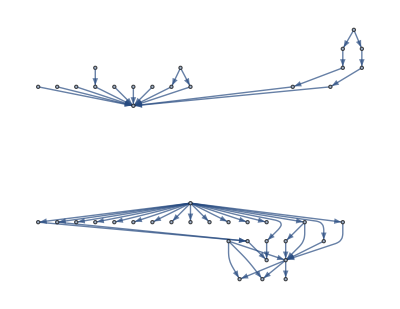

```mathematica
VertexDelete[g,a]
```

## Bug in Weights

```mathematica
RandomWeightedMixedGraph[{vertices_,edges_},threshold_,randomFunction_]/;0<=threshold<=1:=Block[{replaceCount,randomGraph} ,randomGraph=RandomGraph[{vertices,edges}];replaceCount=Floor[threshold edges];randomGraph=Graph[Fold[EdgeAdd[EdgeDelete[#1,#2],First[#2]->Last[#2]]&,randomGraph,RandomSample[EdgeList[randomGraph],replaceCount]]];Graph[randomGraph,EdgeWeight->(Map[#->randomFunction[]&,EdgeList[randomGraph]])]];
```

```mathematica
Table[RandomReal[{1,5}],{k,54}]
```

Table::nliter: Non-list iterator RandomReal[{1,5},#1]& at position 2 does not evaluate to a real numeric value.

Table[𝒢,RandomReal[{1,5},#1]&,{k,54}]

```mathematica
Thread[EdgeList->Table[randomFunction[k],{k,EdgeCount[randomGraph]}]]
```

```mathematica
RandomReal[{1,5},#]&[54]
```

{2.37936,4.48327,2.55579,4.7331,3.81336,2.4517,4.29537,4.02437,1.4431,1.35565,4.13597,2.16305,2.61995,4.51195,2.02093,2.26493,1.00254,3.22101,1.82556,4.01603,2.72883,4.34931,2.92317,3.02759,1.21287,1.05975,4.52097,1.08091,2.9693,1.04245,4.45524,2.10513,2.5118,2.88446,2.39599,2.06981,4.3082,3.85923,3.90576,3.24828,2.83166,4.31984,2.93177,1.59296,3.67457,4.63638,2.83277,1.95455,1.94676,3.40602,3.37535,2.31774,1.09368,3.49859}

## Fixing all the edge weights

```mathematica
RandomWeightedMixedGraph[{vertices_,edges_},threshold_,randomFunction_]/;0<=threshold<=1:=Block[{replaceCount,randomGraph} ,randomGraph=RandomGraph[{vertices,edges}];replaceCount=Floor[threshold edges];randomGraph=Graph[Fold[EdgeAdd[EdgeDelete[#1,#2],First[#2]->Last[#2]]&,randomGraph,RandomSample[EdgeList[randomGraph],replaceCount]]];Graph[randomGraph,EdgeWeight->(Map[#->randomFunction[]&,EdgeList[randomGraph]])]];

RandomWeightedMixedGraph[{vertices_,edges_},threshold_,randomFunction_,k_?IntegerQ]/;0<=threshold<=1:=Table[RandomWeightedMixedGraph[{vertices,edges},threshold,randomFunction],k]

RandomWeightedMixedGraph[{vertices_,edges_},threshold_,randomFunction_,array_List]/;0<=threshold<=1:=Array[RandomWeightedMixedGraph[{vertices,edges},threshold,randomFunction]&,array]

RandomWeightedMixedGraph[graphDistribution_,threshold_,randomFunction_]/;0<=threshold<=1:=Block[{replaceCount,randomGraph} ,randomGraph=RandomGraph[graphDistribution];replaceCount=Floor[threshold EdgeCount[randomGraph]];randomGraph=Graph[Fold[EdgeAdd[EdgeDelete[#1,#2],First[#2]->Last[#2]]&,randomGraph,RandomSample[EdgeList[randomGraph],replaceCount]]];Graph[randomGraph,EdgeWeight->(Map[#->randomFunction[]&,EdgeList[randomGraph]])]];

RandomWeightedMixedGraph[graphDistribution_,threshold_,randomFunction_,k_?IntegerQ]/;0<=threshold<=1∧k>=1:=Table[RandomWeightedMixedGraph[graphDistribution,threshold,randomFunction],k]

RandomWeightedMixedGraph[graphDistribution_,threshold_,randomFunction_,array_List]/;0<=threshold<=1:=Array[RandomWeightedMixedGraph[graphDistribution,threshold,randomFunction]&,array]
```

## Constraints

I need to find the edges and arcs and separate them. I think it would be faster to do this by finding the parts of the adjacency matrix that are not symmetrical.

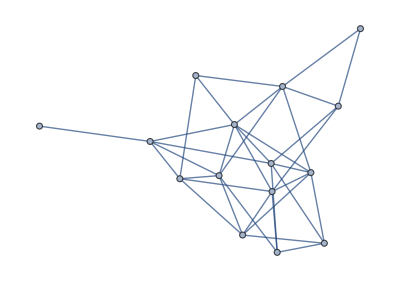

```mathematica
undirectedgraph=RandomMixedGraph[{15,35},0]
```

```mathematica
AdjacencyMatrix[undirectedgraph]
```

SparseArray[…]

```mathematica
AdjacencyMatrix[undirectedgraph]//MatrixForm
```

(0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

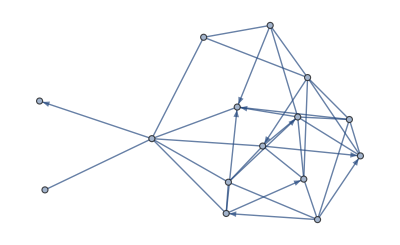

```mathematica
randomMixedGraph=RandomMixedGraph[{15,35},0.5]
```

```mathematica
AdjacencyMatrix[randomMixedGraph]
```

SparseArray[…]

```mathematica
SymmetricMatrixQ[AdjacencyMatrix[randomMixedGraph]]
```

False

## Head

```mathematica
EdgeList[randomMixedGraph]
```

{1->9,1->6,2->8,2->5,3->15,3->14,3->12,4->6,4->11,4->5,6->13,6->15,6->7,7->12,7->8,8->11,12->15,1<->7,1<->8,1<->10,1<->14,1<->15,2<->3,2<->11,2<->13,2<->14,4<->7,4<->13,5<->11,5<->12,5<->15,8<->12,8<->13,11<->12,12<->13}

```mathematica
Cases[EdgeList[randomMixedGraph],_DirectedEdge]
```

{1->9,1->6,2->8,2->5,3->15,3->14,3->12,4->6,4->11,4->5,6->13,6->15,6->7,7->12,7->8,8->11,12->15}

```mathematica
Cases[EdgeList[randomMixedGraph],_UndirectedEdge]
```

{1<->7,1<->8,1<->10,1<->14,1<->15,2<->3,2<->11,2<->13,2<->14,4<->7,4<->13,5<->11,5<->12,5<->15,8<->12,8<->13,11<->12,12<->13}

```mathematica
SimplifiedModel[g_?GraphQ]:=
Block[{res,n,m,a,b,u,v},
n=VertexCount[g];(*I understand this line*)

m=Transpose[IncidenceMatrix[g]];(*I don't understand what this line is for I understand what the incidence matrix represents and what the transpose of a matrix represents but I don't understand what this does.*)
(*a=UnitStep[m-1];(*remove negative values from directed edges/arcs.*)
b=a-m;(*constraints*)*)
res=LinearOptimization[-Total[u+v](*I understand this objective function and the linear optimization*),{u+v \[VectorGreaterEqual]1(*I understand this as saying *)(*,a.u +b.v\[VectorLessEqual]1,a.v +b.u\[VectorLessEqual]1,Total[u]\[VectorGreaterEqual]1,Total[v]\[VectorGreaterEqual]1,u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0,u\[VectorLessEqual]1,v\[VectorLessEqual]1*),u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0,Sum[u-v,{k,Select[First[#]==1&][Cases[EdgeList@randomMixedGraph,_UndirectedEdge]]}],{u∈Vectors[n,Integers],v∈Vectors[n,Integers]}]
(*VertexList[g][[Flatten[Position[Total[{u,v} /. res],0]]*)]
```

```mathematica
SimplifiedModel[undirectedgraph]
```

LinearOptimization::ubnd: The problem is unbounded.

{u→{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},v→{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}}

```mathematica
Names["*Degree*"]
```

{Degree,DegreeCentrality,DegreeGraphDistribution,DegreeLexicographic,DegreeReverseLexicographic,MeanDegreeConnectivity,MeanNeighborDegree,SplineDegree,VertexDegree,VertexInDegree,VertexOutDegree,$MaxRootDegree}

```mathematica
Select[First[#]==1&][Cases[EdgeList@randomMixedGraph,_UndirectedEdge]]
```

{1<->7,1<->8,1<->10,1<->14,1<->15}

```mathematica
Names["*Adjacency*"]
```

{AdjacencyGraph,AdjacencyList,AdjacencyMatrix,WeightedAdjacencyGraph,WeightedAdjacencyMatrix}

```mathematica
AssociationThread[Range[VertexCount[-Graphics-]]->AdjacencyList[-Graphics-]]
```

<|1→{3,4,6},2→{4,5,7},3→{1,5,8},4→{1,2,9},5→{2,3,10},6→{1,7,10},7→{2,6,8},8→{3,7,9},9→{4,8,10},10→{5,6,9}|>

```mathematica
AdjacencyList[-Graphics-, 1]
```

A list of edges incident to vertex 1:

```mathematica
IncidenceList[-Graphics-,1]
```

{1<->3,1<->4,1<->6}

```mathematica
u={a,b,c};
v={d,e,f};
```

## Incidence List

```mathematica
u.IncidenceList[-Graphics-,1]-v.IncidenceList[-Graphics-,1]==0
```

a (1<->3)-d (1<->3)+b (1<->4)-e (1<->4)+c (1<->6)-f (1<->6)==0

```mathematica
u.IncidenceList[-Graphics-,1]-v.IncidenceList[-Graphics-,1]
```

```mathematica
u.IncidenceList[-Graphics-,1]-v.IncidenceList[-Graphics-,1]==0
```

a (1<->3)-d (1<->3)+b (1<->4)-e (1<->4)+c (1<->6)-f (1<->6)==0

```mathematica
u={a,b,c,g}
```

```mathematica
Position[EdgeList[-Graphics-],1<->_]
```

{{1},{2},{3}}

```mathematica
Extract[EdgeList[-Graphics-],Position[EdgeList[-Graphics-],1<->_]]
```

{1<->3,1<->4,1<->6}

## Function

```mathematica
SimplifiedVertexModel[g_?GraphQ]:=Block[{res,n,m,a,b,u,v},
n=VertexCount[g];
m=Transpose[IncidenceMatrix[g]];
res=LinearOptimization[-Total[u+v](*I understand this objective function and the linear optimization*),{u+v \[VectorGreaterEqual]1(*I understand this as saying *)(*,a.u +b.v\[VectorLessEqual]1,a.v +b.u\[VectorLessEqual]1,Total[u]\[VectorGreaterEqual]1,Total[v]\[VectorGreaterEqual]1,u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0,u\[VectorLessEqual]1,v\[VectorLessEqual]1*),u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0,Echo[Extract[u,Position[EdgeList[g],#<->_]].IncidenceList[g,#]-Extract[v,Position[EdgeList[g],#<->_]].IncidenceList[g,#]&/@VertexList[g]==ConstantArray[0,VertexCount[g]]]},{u∈Vectors[n,Integers],v∈Vectors[n,Integers]}]]
```

```mathematica
Extract[,Position[EdgeList[-Graphics-],1<->_]]
```

```mathematica
SimplifiedVertexModel[undirectedgraph]
```

Extract::partd: Part specification {1} is longer than depth of object.

General::stop: Further output of Extract::partd will be suppressed during this calculation.

Dot::dotsh: Tensors {} and {1<->14,6<->14,9<->14,11<->14,12<->14,13<->14} have incompatible shapes.

Dot::dotsh: Tensors {} and {11<->15} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

LinearOptimization::cteqna: The equality constraint … is nonlinear. Equality constraints must be affine.

Extract::partw: Part 4 of {a,b,c} does not exist.

Extract::partw: Part 4 of {d,e,f} does not exist.

Extract::partw: Part 5 of {a,b,c} does not exist.

General::stop: Further output of Extract::partw will be suppressed during this calculation.

LinearOptimization::bdspec: The argument {False,False} at position 3 of LinearOptimization[-a-b-c-d-e-f,«1»,{False,False}] should be a specification for either variables, equality constraints, domains, or solution properties.

LinearOptimization[-a-b-c-d-e-f,{{a+d,b+e,c+f}\[VectorGreaterEqual]1,{a,b,c}\[VectorGreaterEqual]0,{d,e,f}\[VectorGreaterEqual]0,{Extract[{a,b,c},{{1},{2},{3},{4}}].{1<->3,1<->6,1<->10,1<->14}-Extract[{d,e,f},{{1},{2},{3},{4}}].{1<->3,1<->6,1<->10,1<->14},Extract[{a,b,c},{{5},{6},{7},{8},{9},{10}}].{2<->3,2<->5,2<->7,2<->9,2<->12,2<->13}-Extract[{d,e,f},{{5},{6},{7},{8},{9},{10}}].{2<->3,2<->5,2<->7,2<->9,2<->12,2<->13},Extract[{a,b,c},{{11},{12},{13},{14}}].{1<->3,2<->3,3<->4,3<->8,3<->11,3<->13}-Extract[{d,e,f},{{11},{12},{13},{14}}].{1<->3,2<->3,3<->4,3<->8,3<->11,3<->13},Extract[{a,b,c},{{15},{16},{17},{18}}].{3<->4,4<->6,4<->8,4<->10,4<->12}-Extract[{d,e,f},{{15},{16},{17},{18}}].{3<->4,4<->6,4<->8,4<->10,4<->12},Extract[{a,b,c},{{19}}].{2<->5,5<->9}-Extract[{d,e,f},{{19}}].{2<->5,5<->9},Extract[{a,b,c},{{20},{21}}].{1<->6,4<->6,6<->12,6<->14}-Extract[{d,e,f},{{20},{21}}].{1<->6,4<->6,6<->12,6<->14},Extract[{a,b,c},{{22},{23}}].{2<->7,7<->8,7<->13}-Extract[{d,e,f},{{22},{23}}].{2<->7,7<->8,7<->13},Extract[{a,b,c},{{24},{25}}].{3<->8,4<->8,7<->8,8<->10,8<->11}-Extract[{d,e,f},{{24},{25}}].{3<->8,4<->8,7<->8,8<->10,8<->11},Extract[{a,b,c},{{26},{27}}].{2<->9,5<->9,9<->10,9<->14}-Extract[{d,e,f},{{26},{27}}].{2<->9,5<->9,9<->10,9<->14},Extract[{a,b,c},{{28},{29}}].{1<->10,4<->10,8<->10,9<->10,10<->12,10<->13}-Extract[{d,e,f},{{28},{29}}].{1<->10,4<->10,8<->10,9<->10,10<->12,10<->13},Extract[{a,b,c},{{30},{31},{32}}].{3<->11,8<->11,11<->13,11<->14,11<->15}-Extract[{d,e,f},{{30},{31},{32}}].{3<->11,8<->11,11<->13,11<->14,11<->15},Extract[{a,b,c},{{33},{34}}].{2<->12,4<->12,6<->12,10<->12,12<->13,12<->14}-Extract[{d,e,f},{{33},{34}}].{2<->12,4<->12,6<->12,10<->12,12<->13,12<->14},Extract[{a,b,c},{{35}}].{2<->13,3<->13,7<->13,10<->13,11<->13,12<->13,13<->14}-Extract[{d,e,f},{{35}}].{2<->13,3<->13,7<->13,10<->13,11<->13,12<->13,13<->14},0,0}=={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{False,False}]

```mathematica
SimplifiedVertexModel[undirectedgraph]
```

Extract::partd: Part specification {1} is longer than depth of object.

General::stop: Further output of Extract::partd will be suppressed during this calculation.

Dot::dotsh: Tensors {} and {1<->14,6<->14,9<->14,11<->14,12<->14,13<->14} have incompatible shapes.

Dot::dotsh: Tensors {} and {11<->15} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

{Extract[u,{{1},{2},{3},{4}}].{1<->3,1<->6,1<->10,1<->14}-Extract[v,{{1},{2},{3},{4}}].{1<->3,1<->6,1<->10,1<->14},Extract[u,{{5},{6},{7},{8},{9},{10}}].{2<->3,2<->5,2<->7,2<->9,2<->12,2<->13}-Extract[v,{{5},{6},{7},{8},{9},{10}}].{2<->3,2<->5,2<->7,2<->9,2<->12,2<->13},Extract[u,{{11},{12},{13},{14}}].{1<->3,2<->3,3<->4,3<->8,3<->11,3<->13}-Extract[v,{{11},{12},{13},{14}}].{1<->3,2<->3,3<->4,3<->8,3<->11,3<->13},Extract[u,{{15},{16},{17},{18}}].{3<->4,4<->6,4<->8,4<->10,4<->12}-Extract[v,{{15},{16},{17},{18}}].{3<->4,4<->6,4<->8,4<->10,4<->12},Extract[u,{{19}}].{2<->5,5<->9}-Extract[v,{{19}}].{2<->5,5<->9},Extract[u,{{20},{21}}].{1<->6,4<->6,6<->12,6<->14}-Extract[v,{{20},{21}}].{1<->6,4<->6,6<->12,6<->14},Extract[u,{{22},{23}}].{2<->7,7<->8,7<->13}-Extract[v,{{22},{23}}].{2<->7,7<->8,7<->13},Extract[u,{{24},{25}}].{3<->8,4<->8,7<->8,8<->10,8<->11}-Extract[v,{{24},{25}}].{3<->8,4<->8,7<->8,8<->10,8<->11},Extract[u,{{26},{27}}].{2<->9,5<->9,9<->10,9<->14}-Extract[v,{{26},{27}}].{2<->9,5<->9,9<->10,9<->14},Extract[u,{{28},{29}}].{1<->10,4<->10,8<->10,9<->10,10<->12,10<->13}-Extract[v,{{28},{29}}].{1<->10,4<->10,8<->10,9<->10,10<->12,10<->13},Extract[u,{{30},{31},{32}}].{3<->11,8<->11,11<->13,11<->14,11<->15}-Extract[v,{{30},{31},{32}}].{3<->11,8<->11,11<->13,11<->14,11<->15},Extract[u,{{33},{34}}].{2<->12,4<->12,6<->12,10<->12,12<->13,12<->14}-Extract[v,{{33},{34}}].{2<->12,4<->12,6<->12,10<->12,12<->13,12<->14},Extract[u,{{35}}].{2<->13,3<->13,7<->13,10<->13,11<->13,12<->13,13<->14}-Extract[v,{{35}}].{2<->13,3<->13,7<->13,10<->13,11<->13,12<->13,13<->14},0,0}=={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

LinearOptimization::cteqna: The equality constraint … is nonlinear. Equality constraints must be affine.

LinearOptimization[-Total[u+v],{u+v\[VectorGreaterEqual]1,u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0,{Extract[u,{{1},{2},{3},{4}}].{1<->3,1<->6,1<->10,1<->14}-Extract[v,{{1},{2},{3},{4}}].{1<->3,1<->6,1<->10,1<->14},Extract[u,{{5},{6},{7},{8},{9},{10}}].{2<->3,2<->5,2<->7,2<->9,2<->12,2<->13}-Extract[v,{{5},{6},{7},{8},{9},{10}}].{2<->3,2<->5,2<->7,2<->9,2<->12,2<->13},Extract[u,{{11},{12},{13},{14}}].{1<->3,2<->3,3<->4,3<->8,3<->11,3<->13}-Extract[v,{{11},{12},{13},{14}}].{1<->3,2<->3,3<->4,3<->8,3<->11,3<->13},Extract[u,{{15},{16},{17},{18}}].{3<->4,4<->6,4<->8,4<->10,4<->12}-Extract[v,{{15},{16},{17},{18}}].{3<->4,4<->6,4<->8,4<->10,4<->12},Extract[u,{{19}}].{2<->5,5<->9}-Extract[v,{{19}}].{2<->5,5<->9},Extract[u,{{20},{21}}].{1<->6,4<->6,6<->12,6<->14}-Extract[v,{{20},{21}}].{1<->6,4<->6,6<->12,6<->14},Extract[u,{{22},{23}}].{2<->7,7<->8,7<->13}-Extract[v,{{22},{23}}].{2<->7,7<->8,7<->13},Extract[u,{{24},{25}}].{3<->8,4<->8,7<->8,8<->10,8<->11}-Extract[v,{{24},{25}}].{3<->8,4<->8,7<->8,8<->10,8<->11},Extract[u,{{26},{27}}].{2<->9,5<->9,9<->10,9<->14}-Extract[v,{{26},{27}}].{2<->9,5<->9,9<->10,9<->14},Extract[u,{{28},{29}}].{1<->10,4<->10,8<->10,9<->10,10<->12,10<->13}-Extract[v,{{28},{29}}].{1<->10,4<->10,8<->10,9<->10,10<->12,10<->13},Extract[u,{{30},{31},{32}}].{3<->11,8<->11,11<->13,11<->14,11<->15}-Extract[v,{{30},{31},{32}}].{3<->11,8<->11,11<->13,11<->14,11<->15},Extract[u,{{33},{34}}].{2<->12,4<->12,6<->12,10<->12,12<->13,12<->14}-Extract[v,{{33},{34}}].{2<->12,4<->12,6<->12,10<->12,12<->13,12<->14},Extract[u,{{35}}].{2<->13,3<->13,7<->13,10<->13,11<->13,12<->13,13<->14}-Extract[v,{{35}}].{2<->13,3<->13,7<->13,10<->13,11<->13,12<->13,13<->14},0,0}=={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{u∈Vectors[15,ℤ],v∈Vectors[15,ℤ]}]

```mathematica
ClearAll[u,v]
```